```mathematica
data = Import["C:\\Users\\Alexey\\Downloads\\Imitator.csv", "Table"];
```

```mathematica
data
```

{{0,0,0,57584,0,40.2881,33.9323,39.7358,38.3016,40.0735,41.2858,35.061,40.669,40.5607,46.4601},2399,{1}}
 |  |  |  |

```mathematica
data = data[[;;2401, 6;;15]]
```

{{40.2881,33.9323,39.7358,38.3016,40.0735,41.2858,35.061,40.669,40.5607,46.4601},2399,{1}}
 |  |  |  |

```mathematica
traindata = data[[ ;;1600]];
validata = data[[1601;;2000]];
testdata = data[[2001;;]];
```

```mathematica
trainset=Table[Drop[traindata,None,1][[i]]->Flatten[Take[traindata,All,1]][[i]],{i,1,Length[traindata]}];
testset=Table[Drop[testdata,None,1][[i]]->Flatten[Take[testdata,All,1]][[i]],{i,1,Length[testdata]}];
validset=Table[Drop[validata,None,1][[i]]->Flatten[Take[validata,All,1]][[i]],{i,1,Length[validata]}];
```

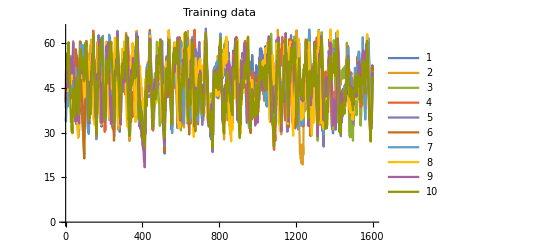
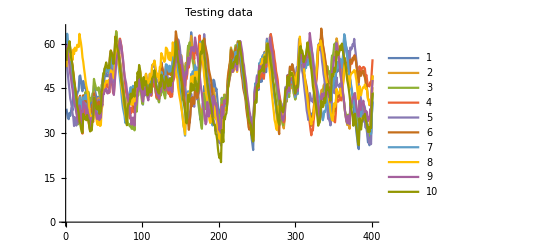
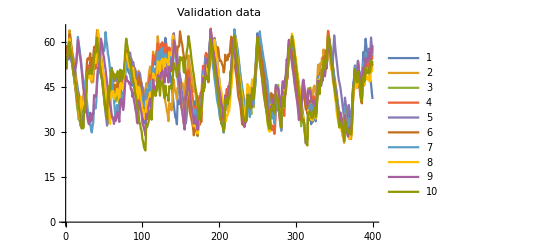

```mathematica
{ListLinePlot[Transpose[traindata],PlotLegends->{"1","2","3","4","5","6","7","8","9","10"},PlotLabel->Style["Training data",15]],ListLinePlot[Transpose[testdata],PlotLegends->{"1","2","3","4","5","6","7","8","9","10"},PlotLabel->Style["Testing data",15]],ListLinePlot[Transpose[validata],PlotLegends->{"1","2","3","4","5","6","7","8","9","10"},PlotLabel->Style["Validation data",15]]}
```

```mathematica
pred=Predict[trainset,ValidationSet->validset,Method->"RandomForest",PerformanceGoal->"Quality"]
```

PredictorFunction[…]

```mathematica
PredictorInformation[pred]
```

Predictor information
Input type | NumericalVector (length: 9)
Method | RandomForest
Standard deviation | 2.85 ± 0.11
Loss | 2.6 ± 0.013
Evaluation time | 55.3 µs/example
Predictor memory | 637. kB
Training examples used | 1600 examples
Training time | 8.64 s
 |

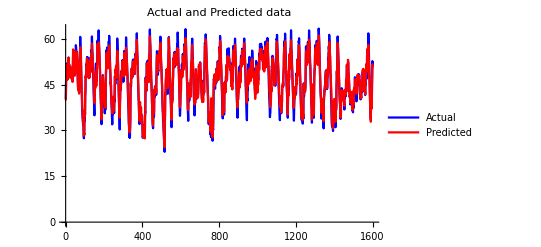

```mathematica
plotdata=Drop[traindata,None,1];
adata=Transpose[Take[traindata,All,1]]//Flatten;
pdata=Table[pred[plotdata[[i]]],{i,1,Length[traindata]}];
ListLinePlot[{adata,pdata},PlotLabel->Style["Actual and Predicted data",15],PlotLegends->{"Actual","Predicted"},PlotStyle->{Blue,Red}]
```

```mathematica
pm=PredictorMeasurements[pred,testset]
```

PredictorMeasurementsObject[…]

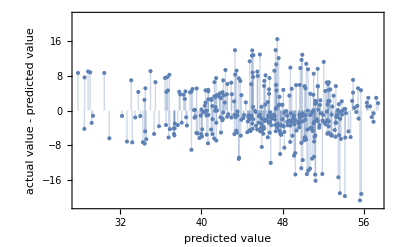

```mathematica
pm["ResidualPlot"]
```

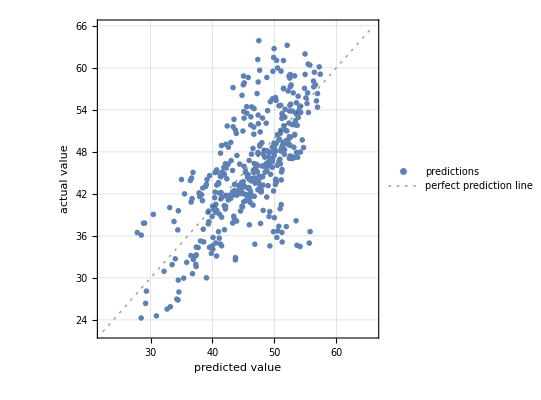

```mathematica
pm["ComparisonPlot"]
```

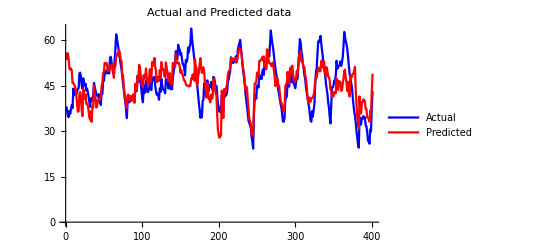

```mathematica
plottestdata=Drop[testdata,None,1];
atestdata=Transpose[Take[testdata,All,1]]//Flatten;
ptestdata=Table[pred[plottestdata[[i]]],{i,1,Length[testdata]}];
ListLinePlot[{atestdata,ptestdata},PlotLabel->Style["Actual and Predicted data",15],PlotLegends->{"Actual","Predicted"},PlotStyle->{Blue,Red}]
```